# NG^21 P_07. Обучение SVM последовательным методом активных ограничений (IncAS)

## 1. Зона влияния радиально - базисной функции Гаусса.

```mathematica
SetDirectory@NotebookDirectory[];Dimensions[Train =DeleteCases[Rest@Import["NG21P07Problem.xlsx",{"Sheets","Бельская Екатерина"}],{"","",""}]]
```

```mathematica
X=Train⟦All,1;;2⟧;
```

```mathematica
Y=Train⟦All,3⟧;
```

```mathematica
ClearAll[K];
K = Compile[
{{x,_Real,1},{y,_Real,1}},
Exp[-((x-y).(x-y))/(2 σ^2)],
Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed",CompilationTarget->"C"
];
```

```mathematica
σ=Mean[StandardDeviation[X]]
```

1.82293

```mathematica
ClearAll[SVM];
SVM[x_List]:=Total[λ*yt*(K[#,x]&/@xt)]-w0;
```

```mathematica
Λ= {λ1,λ2,λ3,λ4};
```

```mathematica
xt = X⟦1;;5⟧;
yt= Y⟦1;;5⟧;
w0 = 0;
```

С увеличением σ зона вокруг опорных точек увеличивается, при уменьшении соответственно сужается.

## 2. Последовательный метод активных ограничений (IncAS)

```mathematica
Map[Dimensions,{iCold=First[#]&/@Position[Train,-1.],
iWarm=First[#]&/@Position[Train, 1.]}]
```

{{1276},{1255}}

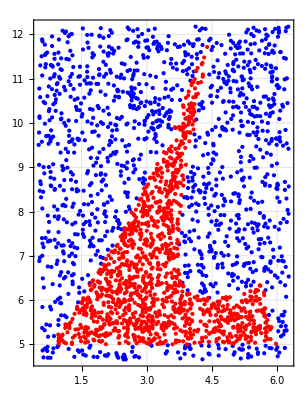

```mathematica
Fig0=Graphics[{Blue,Point@X⟦iCold⟧,Red, Point@X⟦iWarm⟧},Frame->True,GridLines->Automatic]
```

```mathematica
ClearAll[kmIncAS];
kmIncAS[σ_,C_,counter_]:=Monitor[kmInit[σ,C,counter];
While[0<State,Switch[State,
1(*SVM*), kmSolveQP[];SVM=kmSVM[kmW0[]];Step++;State=2;Fig=kmFig[],
2(*S->O*),State=If[kmCheck@"SO",3,1],
3(*S->C*), State=If[kmCheck@"SC",4,1],
4(*O->S*),State=If[kmCheck@"OS",5,1],
5(*C->S*),State=If[kmCheck@"CS",0,1]
]];Fig,Fig]
```

1. Исходные данные : X - координаты точек, Y - соответствующие метки, iCold - номера точек из холодного класса, iWarm - номера точек из горячего класса, Fig0 - график всех точек, раскрашенных на основании принадлежности к какому - либо классу

2. Входные параметры : σ - среднеквадратическое отклонение для функции Гаусса (ядро), С - "цена" штрафа, counter - количество итераций для задания пар опорных точек

3. Процедурные блоки :
   kmIncAS - процедура обучения классификатора
kmInit - процедура инициализация начальных данных
kmKer - процедура идентификации ядра
kmSVM - SVM классификатор
kmW0 - процедура нахождения w0
kmFig - процедура построения карты разделяющей полосы
kmProblemQP - процедура генерации условия задачи квадратичного программирования
kmSolveQP - процедура нахождения решения задачи квадратичного программирования
kmMargin - процедура вычисления отступов
kmCheck - процедура проверки корректности текущего множества точек

4. Глобальные переменные
State - текущий статус выполнения алгоритма
Step - шаг выполнения
σ - среднеквадратическое отклонение
surCharge - "цена" штрафа
Fig - карта разделяющей полосы
Ker - ядро
iS - множество опорных точек
iC - множество точек - нарушителей
iO - множество внутренних точек
λ - символьные переменные для обозначения множителей
λS - множители Лагранжа

## 3. Инициализация

```mathematica
ClearAll[kmInit];
kmInit[Sigma_,C_,counter_]:=(State=1;Step=0;σ=Sigma;surCharge=C;Fig=Fig0;
Ker=kmKer[Sigma];
iS=kmSupport[counter];
iC={};
iO=Complement[Range[Length@X],iS,iC];
λ=ToExpression[StringJoin["λ",ToString[#]]&/@Range[Length[iS]]];
);
```

```mathematica
iS
```

{5,74,510,559,586,760,951,952,1063,1231,1315,1383,1393,1449,1479,1514,1585,1611,1614,1748,1818,1865,2015,2145,2179,2372,2491,2521}

```mathematica
λ=ToExpression[StringJoin["λ",ToString[#]]&/@Range[Length[iS]]]
```

{λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8,λ9,λ10,λ11,λ12,λ13,λ14,λ15,λ16,λ17,λ18,λ19,λ20,λ21,λ22,λ23,λ24,λ25,λ26,λ27,λ28}

```mathematica
kmInit[1,1000,20]
```

```mathematica
kmSolveQP[]
```

{104703.,-10000.,-10000.,-2546.96,44937.6,-5998.,11665.7,-5803.64,30544.7,-10000.,-3190.38,-10000.,-10000.,-10000.,-4948.75,-8926.18,92933.1,-10000.,-6811.63,123149.,-10000.,-10000.,-10000.,85641.8,-10000.,-3988.53,48073.9,36114.4}

```mathematica
SVM=kmSVM[kmW0[]];
```

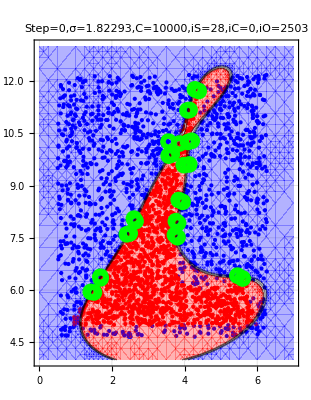

```mathematica
kmFig[]
```

```mathematica
ClearAll[kmKer];
kmKer[σ_]:=Compile[{{x,_Real, 1},{y,_Real, 1}},Exp[(-(x-y).(x-y))/(2 σ^2)], Parallelization->True, RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"];
```

```mathematica
kmKer[3][X⟦1⟧,X⟦2⟧]
```

0.593199

```mathematica
m=Mean[X];
```

```mathematica
m
```

{3.3914,7.85696}

```mathematica
Plot3D[kmKer[σ][{x,y},m],{x,0,7},{y,4,13},PlotRange->Full,ColorFunction->"ThermometerColors"]
```

-Graphics3D-

```mathematica
ClearAll[kmSupport];
kmSupport[]:=Module[{i=1,iSC, iSW,l},
iSC=First@RandomChoice[iCold,1];
iSW=First@Nearest[X⟦iWarm⟧->"Index",X⟦iSC⟧];
l={iSC, iSW};
While[True,If[i==1,iSC=First@Nearest[X⟦iCold⟧->"Index",X⟦iWarm⟧⟦iSW⟧];i--,iSW=First@Nearest[X⟦iWarm⟧->"Index",X⟦iCold⟧⟦iSC⟧];i++];l=Join[l,{iSC,iSW}];
If[l⟦-1⟧==l⟦-3⟧ && l⟦-2⟧==l⟦-4⟧,Break[],Continue[]]];
Flatten[Position[X,#]&/@{X⟦iCold⟧⟦iSC⟧,X⟦iWarm⟧⟦iSW⟧}]]
```

```mathematica
kmSupport[counter_]:=Module[{iS={}},Do[iS=Union[iS,kmSupport[]],counter];iS]
```

```mathematica
kmSupport[30]
```

{5,62,74,83,141,149,248,258,301,381,488,492,510,586,683,697,760,769,794,806,951,952,1023,1063,1238,1294,1392,1393,1421,1449,1479,1525,1526,1664,1748,1865,1948,2015,2178,2289,2315,2372,2481,2521}

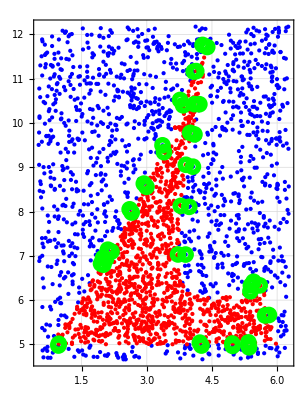

```mathematica
Show[Fig0,Graphics[{Green,AbsoluteThickness@4,Circle[#,Offset@4]&/@X⟦kmSupport[30]⟧}]]
```

## 4. SVM - классификатор и карта разделяющей полосы

```mathematica
ClearAll[kmSVM];
kmSVM[w0_]:=With[{ΛYsc=Join[λS Y⟦iS⟧,surCharge Y⟦iC⟧],Xsc=X⟦Join[iS,iC]⟧},Compile[{{x,_Real,1}},(Ker[#,x]&/@Xsc).ΛYsc-w0,Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed",CompilationTarget->"C"]]
```

```mathematica
kmInit[1,1000,5];
```

```mathematica
λS=RandomReal[{-5,5},Length@iS];SVM = kmSVM[kmW0[]]
```

CompiledFunction[…]

```mathematica
Plot3D[
SVM@{x,y},{x,0,8},{y ,4,13},
ColorFunction->ColorData[{"RedBlueTones","Reverse"}], PlotPoints->10,PlotRange->All,ImageSize->Medium]
```

-Graphics3D-

```mathematica
ClearAll[kmW0];
kmW0[]:=Block[
{iSC = Join[iS,iC],ΛYsc=Join[λS Y⟦iS⟧,surCharge Y⟦iC⟧],Xsc=X⟦Join[iS,iC]⟧,size = Length[Join[iS,iC]]},
Median[
(ParallelSum[ΛYsc⟦s⟧*Ker[Xsc⟦s⟧,#],{s,size}]&/@Xsc)-Y⟦iSC⟧
]
];
```

```mathematica
ClearAll[kmFig];
kmFig[]:=Show[Fig0,ContourPlot[SVM@{x1,x2},{x1,0.4,6.2},{x2,4.5,12.2},Contours->{-1,0,1},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0],Hue[0,1,1,0.3]}],Graphics[  {Green, AbsoluteThickness@4,Circle[#,Offset@4]&/@X⟦iS⟧,Gray,Circle[#,Offset@4]&/@X⟦iC⟧}],PlotLabel->StringForm["Step=``,σ=``,C=``,iS=``,iC=``,iO=``",Step,σ,surCharge,Length@iS,Length@iC,Length@iO]]
```

```mathematica
kmInit[σ,1000,20]
```

```mathematica
kmSolveQP[]
```

{-1000.,-1000.,6149.61,10446.7,-419.264,-126.577,-1000.,306.484,-1000.,454.791,208.928,-1000.,1236.91,220.323,-783.114,408.655,-82.7396,239.285,7501.08,534.954,-1000.,243.735,2389.78,-205.141,5564.94,168.376,740.565,-1000.,494.715,1422.42}

```mathematica
SVM=kmSVM[kmW0[]];
```

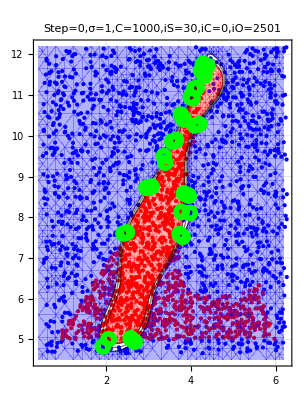

```mathematica
kmFig[]
```

## 5. Решение задачи квадратичного программирования

```mathematica
ClearAll[kmSolveQP];
kmSolveQP[]:=(λ= ToExpression[StringJoin["λ",ToString[#]]&/@Range[Length[iS]]];λS=Values@Last@FindMinimum[kmProblemQP[],λ]);
```

```mathematica
ClearAll[kmProblemQP];
kmProblemQP[]:=(
Qss=ParallelArray[Y⟦iS⟦#1⟧⟧*Y⟦iS⟦#2⟧⟧*Ker[X⟦iS⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iS,Length@iS}];
Qcs=ParallelArray[Y⟦iC⟦#1⟧⟧*Y⟦iS⟦#2⟧⟧*Ker[X⟦iC⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iC,Length@iS}];
{1/2 Qss.λ.λ +If[Length@Qcs>0,surCharge*Total[Qcs.λ],0]-Total[λ],
Y⟦iS⟧.λ+surCharge*Total[Y⟦iC⟧]==0 && And@@(-surCharge≤ #&/@λ)})
```

```mathematica
kmSolveQP[]
```

{3271.21,4059.53,365.731,1338.31,-1000.,-1000.,-104.712,142.394,-1000.,-349.798,-1000.,1562.14,-18.965,150.109,-462.542,-458.853,381.892,4118.6,-1000.,-1000.,-1000.,1193.75,2840.46,-862.228,1789.34,-1000.}

## 6. Корректировка множества опорных точек

```mathematica
ClearAll[kmCheck];
kmCheck["SO"]:=If[(iBad=Flatten@Position[λS,i_/;i<=0])=={},True,iBad=RandomChoice[Abs@λS⟦iBad⟧->iBad];
AppendTo[iO,iS⟦iBad⟧];
iS=Delete[iS,iBad];
False];
```

```mathematica
kmCheck["SC"]:=If[(iBad=Flatten@Position[λS,i_/;i≥ surCharge])=={},True,iBad=RandomChoice[(λS⟦iBad⟧-surCharge)->iBad];
AppendTo[iC,iS⟦iBad⟧];
iS=Delete[iS,iBad];
False];
```

## 7. Проверка отступа неопорных точек

```mathematica
ClearAll[kmMargin];
kmMargin[ind_]:=Y⟦ind⟧SVM[X⟦ind⟧]
SetAttributes[kmMargin,Listable]
```

```mathematica
kmMargin[{1,2,3,4}]
```

{-0.683369,2.80188,-2.65795,-0.560455}

```mathematica
kmCheck["OS"]:=If[margins=kmMargin[iO];(iBad=Flatten@Position[margins,i_/;i≤1])=={},True,
iBad=RandomChoice[Abs[1-margins⟦iBad⟧]->iBad];
AppendTo[iS,iO⟦iBad⟧];
iO=Delete[iO,iBad];
False];
```

```mathematica
kmCheck["CS"]:=If[margins=kmMargin[iC];(iBad=Flatten@Position[margins,i_/;i≥ 1])=={},True,
iBad=RandomChoice[Abs[1-margins⟦iBad⟧]->iBad];
AppendTo[iS,iC⟦iBad⟧];
iC=Delete[iC,iBad];
False]
```

```mathematica
ClearAll[λ]
```

## 8. Обучение SVM - классификатора

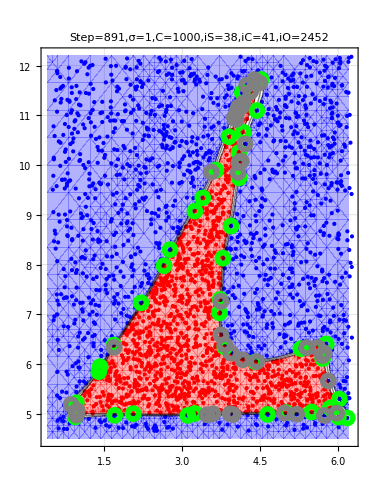

```mathematica
kmIncAS[σ,1000,5]
```

Проверки показывают что чем больше размер штрафа, тем меньше точек - нарушителей, тем точнее будет классификация